```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## Debye mass HTL Fitting

### Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

### Fitting

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
Tclatt=0.1725;
Tccont={0.155,9};
```

```mathematica
md={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}};
σmd={0.2088095376752115,0.21706712111822724,0.22532470456124298,0.23564668386501264,0.2459686631687824,0.2500974548902902,0.26496110508771864};
σmderr={0.01621039222655274,0.015928132568206136,0.015645872909859533,0.015293048336926279,0.014940223763993024,0.014799093934819724,0.014291026549795836};
```

```mathematica
αcont={0.5138562580709736,0.0027118637679895965};
σcont={0.16949622818854412,0.0009172672238755708};
ccont={-0.15942304870711493,0.0023023051670536016};
```

```mathematica
mDfit=NonlinearModelFit[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.503185 | 0.0966623 | 5.2056 | 0.00345094
e | -0.270021 | 0.0394174 | -6.85029 | 0.00101247

```mathematica
mDfitupper=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]+md[[n,2]])/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitupper["BestFitParameters"];
mDfitupper["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.877254 | 0.0664694 | 13.1979 | 0.0000446105
e | -0.383222 | 0.0271052 | -14.1383 | 0.0000318649

```mathematica
mDfitlower=NonlinearModelFit[Table[{T[[n]](155/172.5),(md[[n,1]]-md[[n,2]])/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitlower["BestFitParameters"];
mDfitlower["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.129116 | 0.153394 | 0.841727 | 0.438334
e | -0.156819 | 0.0625515 | -2.50704 | 0.0540234

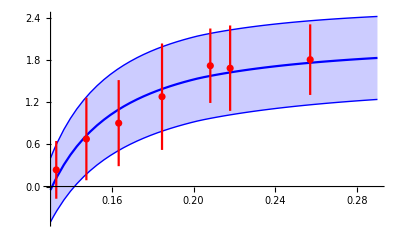

```mathematica
Show[{Plot[{mDcalT[2π,x,k1,k2],mDcalT[2π,x,k1u,k2u],mDcalT[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

```mathematica
mdrandu[n_]:=Module[{m},m=md[[n,1]]+Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
mdrandl[n_]:=Module[{m},m=md[[n,1]]-Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
σrand[n_]:=RandomVariate[NormalDistribution[σmd[[n]],σmderr[[n]]]];
σcontrand:=RandomVariate[NormalDistribution[σcont[[1]],σcont[[2]]]];
```

```mathematica
fitsu={{},{}};
fitsl={{},{}};
SetSharedVariable[fitsu,fitsl];
Module[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandu[n]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{T[[n]](155/172.5),mdrandl[n]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[T]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"]];
fitsu[[1]]=Append[fitsu[[1]],k1u];
fitsu[[2]]=Append[fitsu[[2]],k2u];
fitsl[[1]]=Append[fitsl[[1]],k1l];fitsl[[2]]=Append[fitsl[[2]],k2l],{i,1,100000}]]
```

```mathematica
kfinalu={Mean[fitsu[[1]]],Mean[fitsu[[2]]]}
kfinall={Mean[fitsl[[1]]],Mean[fitsl[[2]]]}
```

{0.801696,-0.360406}

{0.13899,-0.149229}

```mathematica
kfinalu={0.8016955527941704,-0.36040626803845205};
kfinall={0.1389898610341079,-0.14922900812090412};
```

```mathematica
kfinal={Mean[{kfinalu[[1]],kfinall[[1]]}],Mean[{kfinalu[[2]],kfinall[[2]]}]}
```

{0.470343,-0.254818}

```mathematica
kfinal={0.47034270691413915,-0.25481763807967805}(*100k run*)
```

{0.470343,-0.254818}

```mathematica
kerror={kfinalu[[1]]-kfinal[[1]],kfinal[[2]]-kfinalu[[2]]}
```

{0.331353,0.105589}

```mathematica
kerror={0.3313528458800312,0.105588629958774};
```

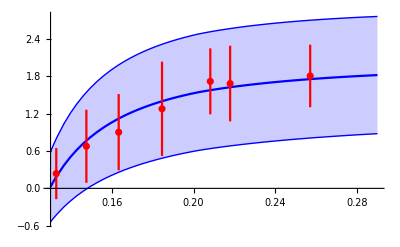

```mathematica
Show[{Plot[{mDcalT[2π,x,kfinal[[1]],kfinal[[2]]],mDcalT[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcalT[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{T[[n]](155/172.5),md[[n,1]]/T[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/T[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4689783072176936;
Mb=4.882;
```

### Define required functions

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
ϵ=1/1000;ϕ1table=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10+1000ϵ,100,10000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,100+100000ϵ,10000,100000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10000+10000000ϵ,1000000,10000000ϵ}]]]];
```

```mathematica
TableT[σ1_,α1_, mD1_]:=Module[{σ=σ1, α=α1,mD=mD1,r,μ,c1},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c1=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]];
ψ1[x_,r_]:=c1-ParabolicCylinderR[x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderI[x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,11,100,1}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,200,1000,100}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,2000,20000,1000}]]];];
```

### Modules

```mathematica
swaveccspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["spectraldata/Tscan/cc/swccT"<>ToString[Tstring]<>"uspectra.dat",ccsT]
]
```

```mathematica
swavebbspectra[n_,Tscan_]:=Module[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,Tstring,ρtable,bbsT},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=3;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];
ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

bbsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];

Tstring=Round[T*1000];
Export["spectraldata/Tscan/bb/swbbT"<>ToString[Tstring]<>"lspectra.dat",bbsT]
]
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.299,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297}

```mathematica
Do[swaveccspectra[i,Tscanc],{i,Length[Tscanc]}]//AbsoluteTiming
```

{10438.7,Null}

```mathematica
Do[swaveccspectra[i,Tscanc],{i,Length[Tscanc]}]//AbsoluteTiming
```

{11613.1,Null}

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}];
```

```mathematica
Do[swavebbspectra[i,Tscanb],{i,Length[Tscanb]}]//AbsoluteTiming
```

{8.×10^-6,Null}

## Continuum Energies

```mathematica
2Mc+Table[ReV[100000,mDcal[2π,Tscancorig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.64855,3.62879,3.61028,3.59287,3.57646,3.56095,3.54624,3.53227,3.51897,3.50628,3.49415,3.47139,3.44048,3.41275,3.38761,3.36462,3.34344,3.32379,3.30545,3.28826,3.27207,3.25675,3.24221,3.22837,3.21514,3.20272,3.19118,3.18002,3.16922,3.15875,3.14858,3.1387,3.12908,3.1197,3.11055,3.10162,3.09288,3.08434,3.07598,3.06778,3.05974,3.05186,3.04411,3.0365,3.02902,3.02166,3.01441,3.00728,3.00025,2.99333,2.9865,2.97976,2.97311,2.96654,2.96006,2.95366,2.94733}

```mathematica
2Mc+Table[ReV[100000,mDcal[2π,Tscancorig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{4.04871,4.00932,3.97357,3.94094,3.91096,3.8833,3.85766,3.8338,3.8115,3.7906,3.77095,3.73492,3.68757,3.64654,3.61046,3.57831,3.54936,3.52306,3.49897,3.47676,3.45615,3.43694,3.41894,3.40201,3.38601,3.3712,3.35764,3.34466,3.33219,3.32019,3.30862,3.29745,3.28666,3.2762,3.26607,3.25623,3.24666,3.23735,3.22829,3.21945,3.21083,3.20241,3.19418,3.18612,3.17824,3.17051,3.16294,3.15552,3.14823,3.14107,3.13404,3.12712,3.12032,3.11363,3.10704,3.10056,3.09416}

```mathematica
2Mc+Table[ReV[100000,mDcal[2π,Tscancorig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.44938,3.43502,3.42139,3.40842,3.39607,3.38426,3.37297,3.36214,3.35173,3.34173,3.33209,3.31382,3.28858,3.26555,3.24434,3.22467,3.20632,3.1891,3.17287,3.1575,3.1429,3.12897,3.11565,3.10288,3.09059,3.07895,3.06803,3.05741,3.04709,3.03703,3.02722,3.01764,3.00828,2.99911,2.99014,2.98135,2.97272,2.96425,2.95593,2.94775,2.93971,2.93179,2.92399,2.91631,2.90874,2.90127,2.8939,2.88662,2.87944,2.87234,2.86532,2.85839,2.85153,2.84474,2.83803,2.83138,2.8248}

```mathematica
2Mb+Table[ReV[100000,mDcal[2π,Tscanborig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.4746,10.387,10.3202,10.2665,10.2218,10.1834,10.1498,10.1199,10.0929,10.0683,10.0455,10.0249,10.0061,9.98825,9.9713,9.95512,9.93962,9.92473,9.91039,9.89654,9.88314,9.87015,9.85754,9.84527,9.83332,9.82167,9.81028,9.79915,9.78826,9.77758,9.76711,9.75683,9.74674,9.73681,9.72705,9.71744,9.70797,9.69863,9.68943,9.68035,9.67138,9.66253,9.65378,9.64513,9.63658,9.62812,9.61975,9.61147,9.60326,9.59514,9.58708,9.5791,9.57119,9.56335,9.55556,9.54784,9.54018,9.53258,9.52503,9.51754,9.5101,9.50271,9.49536,9.48807,9.48082,9.47361,9.46644,9.45932,9.45224,9.4452,9.43819,9.43122,9.42429,9.41739,9.41053,9.4037,9.3969,9.39013,9.3834,9.37669,9.37001,9.36336,9.35674,9.35015,9.34358,9.33704,9.33052,9.32403,9.31756,9.31111,9.30469}

```mathematica
2Mb+Table[ReV[100000,mDcal[2π,Tscanborig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.8748,10.7093,10.597,10.5136,10.4481,10.3944,10.3491,10.31,10.2756,10.245,10.2173,10.1927,10.1707,10.1502,10.1309,10.1127,10.0955,10.0791,10.0634,10.0484,10.034,10.0202,10.0069,9.99402,9.98156,9.96949,9.95776,9.94637,9.93527,9.92446,9.91391,9.9036,9.89352,9.88365,9.87399,9.86451,9.85521,9.84608,9.83711,9.82829,9.81962,9.81107,9.80266,9.79437,9.7862,9.77814,9.77018,9.76233,9.75457,9.74691,9.73933,9.73184,9.72443,9.71711,9.70985,9.70267,9.69556,9.68852,9.68154,9.67463,9.66777,9.66098,9.65424,9.64756,9.64092,9.63434,9.62781,9.62133,9.61489,9.6085,9.60215,9.59585,9.58958,9.58336,9.57717,9.57102,9.56491,9.55883,9.55279,9.54679,9.54081,9.53487,9.52896,9.52308,9.51723,9.5114,9.50561,9.49984,9.4941,9.48839,9.4827}

```mathematica
2Mb+Table[ReV[100000,mDcal[2π,Tscanborig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.2754,10.2103,10.1581,10.1146,10.0773,10.0445,10.0151,9.98858,9.96423,9.9417,9.92068,9.90131,9.88346,9.8664,9.85004,9.83432,9.81915,9.8045,9.79029,9.77651,9.7631,9.75004,9.73729,9.72484,9.71266,9.70074,9.68905,9.67757,9.6663,9.65522,9.64432,9.63359,9.62302,9.6126,9.60232,9.59217,9.58215,9.57225,9.56246,9.55279,9.54321,9.53374,9.52436,9.51507,9.50587,9.49675,9.48771,9.47875,9.46986,9.46104,9.45229,9.4436,9.43498,9.42641,9.41791,9.40946,9.40106,9.39272,9.38443,9.37619,9.368,9.35985,9.35174,9.34368,9.33566,9.32769,9.31975,9.31185,9.30399,9.29616,9.28837,9.28062,9.27289,9.2652,9.25755,9.24992,9.24232,9.23476,9.22722,9.21971,9.21222,9.20477,9.19734,9.18993,9.18255,9.1752,9.16786,9.16056,9.15327,9.14601,9.13876}